## Scattering Rates, for electrons, and for phonons;

#### Get scattering Rates;

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/EPW/ZrC/LDA/"];
temps={"0K","10K","300K","500K","760K","1000K","1500K","1900K","2500K","3200K","3800K"};
scatteringRatesE=Table[ReadList[StringJoin["Variable_Volume/ScatteringRates/constant_smearing/kRandom/",ToString@temps[[i]],"/scattering_rate",ToString@temps[[i]]],{Number, Number,Number, Number,Number}],{i,1,11}];
```

```mathematica
K2eV=8.617332478*10^−5;
```

#### Parse rates and lives;

```mathematica
(*To convert meV to THz, multiply by 3.0385309*10^12*)
```

```mathematica
scatteringRatesE300=ReadList["/Volumes/MicroSD/Dropbox/EPW/ZrC/LDA/Variable_Volume/ScatteringRates/constant_smearing/kRandom/300K/scattering_rate300K",{Number, Number,Number, Number,Number}];
```

```mathematica
scatteringRatesPh300=ReadList["/Volumes/MicroSD/Dropbox/EPW/ZrC/LDA/Variable_Volume/ScatteringRates/constant_smearing/kRandom/300K/ph_scattering_rate_meV_to_ph300K",{Number, Number,Number, Number,Number,Number}];
```

```mathematica
scatteringRatesPh0=ReadList["/Volumes/MicroSD/Dropbox/EPW/ZrC/LDA/Variable_Volume/ScatteringRates/constant_smearing/kRandom/0K/ph_scattering_rate_meV_to_ph0K",{Number, Number,Number, Number,Number,Number}];
```

```mathematica
scatteringRatesPh3800=ReadList["/Volumes/MicroSD/Dropbox/EPW/ZrC/LDA/Variable_Volume/ScatteringRates/constant_smearing/kRandom/3800K/ph_scattering_rate_meV_to_ph3800K",{Number, Number,Number, Number,Number,Number}];
```

```mathematica
scatteringRatesE3800=ReadList["/Volumes/MicroSD/Dropbox/EPW/ZrC/LDA/Variable_Volume/ScatteringRates/constant_smearing/kRandom/3800K/scattering_rate3800K",{Number, Number,Number, Number,Number}];
```

```mathematica
rateData300E=Transpose[{Transpose[scatteringRatesE300][[3]],(10^-12)*Transpose[scatteringRatesE300][[4]]}];
```

```mathematica
rateData3800E=Transpose[{Transpose[scatteringRatesE3800][[3]],(10^-12)*Transpose[scatteringRatesE3800][[4]]}];
```

```mathematica
rateData0Ph=Transpose[{Transpose[scatteringRatesPh0][[5]],Transpose[scatteringRatesPh0][[6]]}];
```

```mathematica
rateData300Ph=Transpose[{Transpose[scatteringRatesPh300][[5]],Transpose[scatteringRatesPh300][[6]]}];
```

```mathematica
rateData3800Ph=Transpose[{Transpose[scatteringRatesPh3800][[5]],Transpose[scatteringRatesPh3800][[6]]}];
```

```mathematica
rateData300E[[1]]
```

{-1.37236,198.29}

```mathematica
rateData300Ph[[1]]
```

{6.67428,0.000946422}

```mathematica
rateData300E5=RandomSample[rateData300E,10^5];
```

```mathematica
rateData3800E5=RandomSample[rateData3800E,10^5];
```

```mathematica
rateData0Ph=Transpose[{Transpose[scatteringRatesPh0][[5]],Transpose[scatteringRatesPh0][[6]]}];
```

```mathematica
rateData0Ph5=RandomSample[rateData0Ph,10^5];
```

```mathematica
rateData300Ph5=RandomSample[rateData300Ph,10^5];
```

```mathematica
rateData3800Ph5=RandomSample[rateData3800Ph,10^5];
```

```mathematica
(*Electron self-energy from electron-phonon coupling*)
```

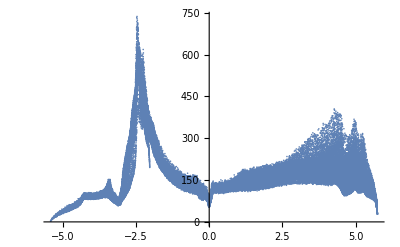

```mathematica
ListPlot@rateData300E5
```

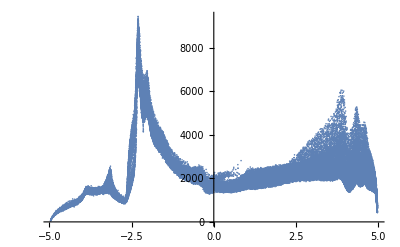

```mathematica
ListPlot@rateData3800E5
```

```mathematica
(*Phonon self-energy from electron-phonon coupling*)
```

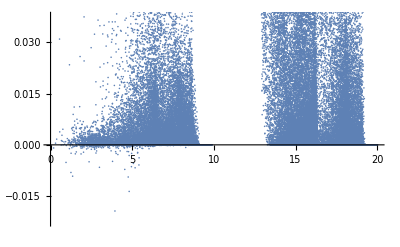

```mathematica
ListPlot@rateData0Ph5
```

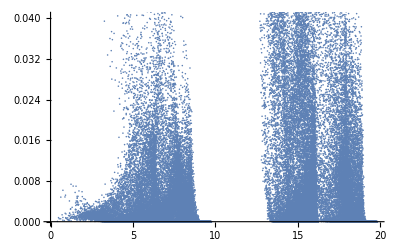

```mathematica
ListPlot@rateData300Ph5
```

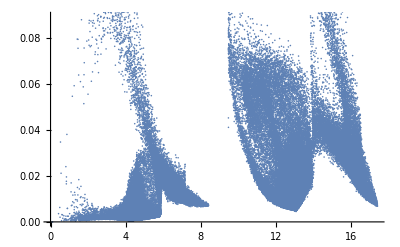

```mathematica
ListPlot@rateData3800Ph5
```

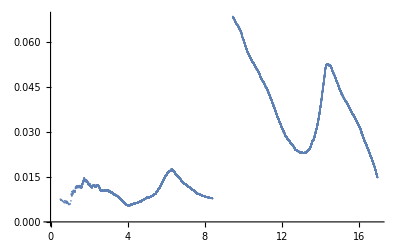

```mathematica
ListPlot@MovingMap[Mean,rateData3800Ph5,{K2eV*(10000),Center}]
```

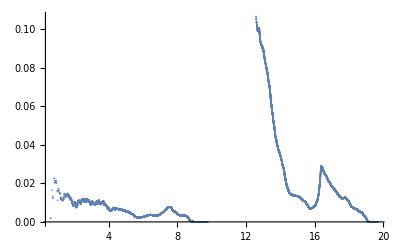

```mathematica
ListPlot[MovingMap[Mean,rateData300Ph5,{K2eV*(4000),Center}],PlotRange->All]
```

```mathematica
data0Ph=MovingMap[Mean,rateData0Ph5,{K2eV*(4000),Center}];
data300Ph=MovingMap[Mean,rateData300Ph5,{K2eV*(4000),Center}];
data3800Ph=MovingMap[Mean,rateData3800Ph5,{K2eV*(4000),Center}];
```

```mathematica
dataPlot=ListPlot[{data0Ph,data300Ph,data3800Ph},PlotRange->All]
```

-Graphics-

```mathematica
partA0=Table[{x/100,0.0},{x,0,Round[Transpose[data0Ph][[1]][[1]]*100]}];
partB0=Table[{x/100,0.0},{x,100*9,Round[100*data[[Position[Transpose[data0Ph][[2]],Max[Transpose[data0Ph][[2]]]][[1]][[1]]]][[1]]]}];
partC0=Table[{x/100,0.0},{x,data0Ph[[-1]][[1]]*100,100*21}];
partA300=Table[{x/100,0.0},{x,0,Round[Transpose[data300Ph][[1]][[1]]*100]}];
partB300=Table[{x/100,0.0},{x,100*9,Round[100*data[[Position[Transpose[data300Ph][[2]],Max[Transpose[data300Ph][[2]]]][[1]][[1]]]][[1]]]}];
partC300=Table[{x/100,0.0},{x,data300Ph[[-1]][[1]]*100,100*21}];
partA3800=Table[{x/100,0.0},{x,0,Round[Transpose[data3800Ph][[1]][[1]]*100]}];
partB3800=Table[{x/100,0.0},{x,100*9,Round[100*data[[Position[Transpose[data3800Ph][[2]],Max[Transpose[data3800Ph][[2]]]][[1]][[1]]]][[1]]]}];
partC3800=Table[{x/100,0.0},{x,data3800Ph[[-1]][[1]]*100,100*21}];
```

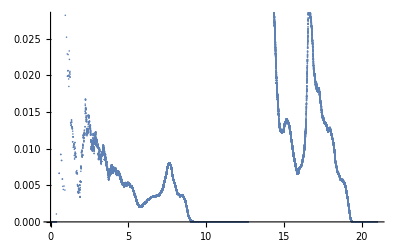

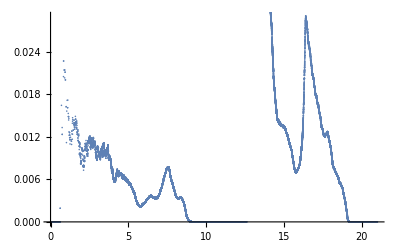

-Graphics-

```mathematica
ListPlot@Sort[Join[partC0,partB0,partA0,data0Ph]]
ListPlot@Sort[Join[partC300,partB300,partA300,data300Ph]]
ListPlot@Sort[Join[partC3800,partB3800,partA3800,data3800Ph]]
```

```mathematica
interData0=Interpolation[MovingAverage[Sort[Join[partC0,partB0,partA0,data0Ph]],20],InterpolationOrder->1]
interData300=Interpolation[MovingAverage[Sort[Join[partC300,partB300,partA300,data300Ph]],20],InterpolationOrder->1]
interData3800=Interpolation[MovingAverage[Sort[Join[partC3800,partB3800,partA3800,data3800Ph]],20],InterpolationOrder->1]
```

InterpolatingFunction[{{0.095, 20.9045}}, <>]

InterpolatingFunction[{{0.095, 20.903}}, <>]

InterpolatingFunction[{{0.095, 20.9022}}, <>]

InterpolatingFunction::dmval: Input value {0.000408571} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

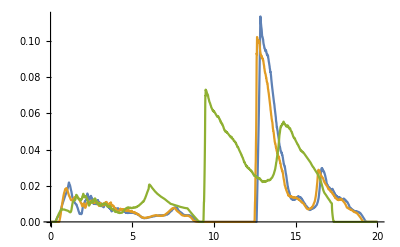

```mathematica
interPlot=Plot[{interData0[x],interData300[x],interData3800[x]},{x,0,20},PlotRange->All]
```

```mathematica
Integrate[{interData0[x],interData300[x],interData3800[x]},{x,0,20}]
```

InterpolatingFunction::dmvali: The integration endpoint 0 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmvali will be suppressed during this calculation.

{0.239129,0.230585,0.382813}

```mathematica
t3emps={"10K","300K","3800K"}
pTops={FrameTicksStyle->20,Frame->True,ImageSize->400,FrameStyle->Directive[Black,Thickness[0.0025]],FrameLabel->{Style["ω (THz)",20,Black],Style["Π'' (THz)",20,Black]},PlotRange->{All,{0,0.12}},AspectRatio->0.66,PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.007]],PlotLegends->Placed[SwatchLegend[Table[Style[t3emps[[i]],18],{i,1,3,1}]],{ 0.15,0.79}]};
```

{10K,300K,3800K}

InterpolatingFunction::dmval: Input value {0.000408571} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

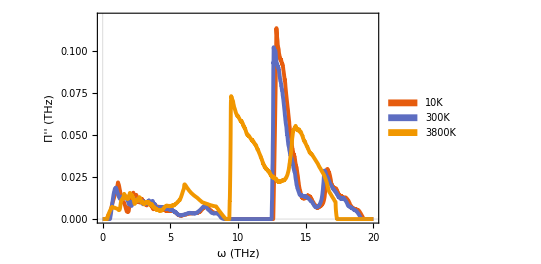

```mathematica
interPlotGood=Plot[{interData0[x],interData300[x],interData3800[x]},{x,0,20},Evaluate@pTops,PlotRange->All]
```

InterpolatingFunction::dmval: Input value {0.000408571} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

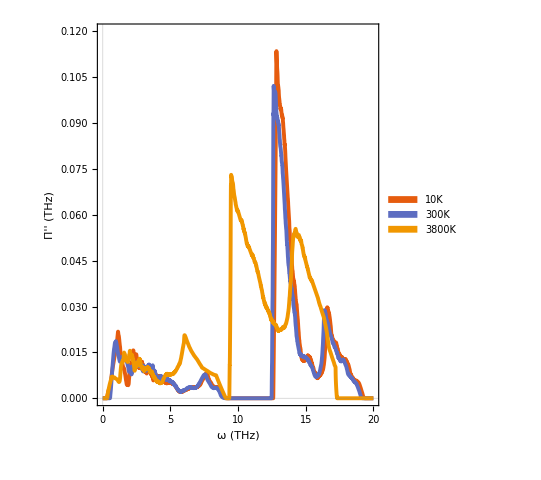

```mathematica
pTops2={FrameTicksStyle->20,Frame->True,ImageSize->400,FrameStyle->Directive[Black,Thickness[0.0025]],FrameLabel->{Style["ω (THz)",20,Black],Style["Π'' (THz)",20,Black]},PlotRange->{All,{0,0.12}},AspectRatio->1.2,PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.007]],PlotLegends->Placed[SwatchLegend[Table[Style[t3emps[[i]],18],{i,1,3,1}]],{ 0.15,0.79}]};
interPlotGood=Plot[{interData0[x],interData300[x],interData3800[x]},{x,0,20},Evaluate@pTops2,PlotRange->All]
```

```mathematica
numericalHT[fun_,y_,upperBound_,singularPointRad_,maxRecursions_,workingPrec_]:=NIntegrate[((-2y)/Pi)*fun[x]/(x^2-y^2),{x,0,upperBound},Method->{"PrincipalValue","SingularPointIntegrationRadius"->singularPointRad},MaxRecursion->maxRecursions,Exclusions->{((x^2)-(y^2))==0},WorkingPrecision->workingPrec]//N
```

```mathematica
numericalHT[interData0,i,Infinity,10^-10,20,5]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
Plot[interData0[x],{x,0,20}]
```

InterpolatingFunction::dmval: Input value {0.000408571} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
imPhH1=Table[{i,numericalHT[interData0,i,Infinity,0.1,20,5]},{i,0,20,0.25}];
```

```mathematica
imPhH1
Show[{ListPlot[imPhH1],ListLinePlot[imPhH1]}]
```

{{0.,0.},{0.25,-0.00395912},{0.5,-0.007968},{0.75,-0.0101063},{1.,-0.00721517},{1.25,0.00468156},{1.5,0.00506281},{1.75,0.00466049},{2.,-0.00375566},{2.25,-0.0000607575},{2.5,0.00511257},{2.75,0.00513045},{3.,0.00446838},{3.25,0.00395975},{3.5,0.00505259},{3.75,0.00410112},{4.,0.00407683},{4.25,0.00377725},{4.5,0.00475597},{4.75,0.00353316},{5.,0.00340004},{5.25,0.00375172},{5.5,0.00346174},{5.75,0.00163846},{6.,0.000392984},{6.25,-0.000329251},{6.5,-0.000847247},{6.75,-0.000966496},{7.,-0.00211482},{7.25,-0.00314055},{7.5,-0.00238877},{7.75,0.000661871},{8.,0.00139034},{8.25,0.000592685},{8.5,0.000379787},{8.75,0.0005643},{9.,-0.00114287},{9.25,-0.00296086},{9.5,-0.00441088},{9.75,-0.00558741},{10.,-0.00697293},{10.25,-0.00826864},{10.5,-0.00985048},{10.75,-0.0115997},{11.,-0.0136152},{11.25,-0.0160418},{11.5,-0.0191972},{11.75,-0.0234175},{12.,-0.0290587},{12.25,-0.0387263},{12.5,-0.0595136},{12.75,-0.107282},{13.,-0.0279258},{13.25,0.000458387},{13.5,0.0270785},{13.75,0.0385605},{14.,0.0411093},{14.25,0.0406474},{14.5,0.0395701},{14.75,0.0298991},{15.,0.0235063},{15.25,0.0224074},{15.5,0.0220235},{15.75,0.018467},{16.,0.0128489},{16.25,0.00739582},{16.5,-0.000170093},{16.75,0.0178188},{17.,0.0212857},{17.25,0.0218992},{17.5,0.0226725},{17.75,0.0226454},{18.,0.0232549},{18.25,0.0249542},{18.5,0.023193},{18.75,0.0221129},{19.,0.0229281},{19.25,0.0216947},{19.5,0.0191739},{19.75,0.0113341},{20.,0.0160149}}

-Graphics-

```mathematica
imPhH2=Table[{i,numericalHT[interData300,i,Infinity,0.1,5,5]},{i,0,20,0.25}];
Show[{ListPlot[imPhH2],ListLinePlot[imPhH2]}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 5 recursive bisections in x near {x} = {10.045}. NIntegrate obtained -0.0032317 and 0.000080791 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 5 recursive bisections in x near {x} = {10.795}. NIntegrate obtained -0.010985 and 0.00022813 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 5 recursive bisections in x near {x} = {11.295}. NIntegrate obtained -0.011162 and 0.00026155 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

```mathematica
imPhH2a=Table[{i,numericalHT[interData300,i,Infinity,0.1,10,5]},{i,0,20,0.25}];
Show[{ListPlot[imPhH2a],ListLinePlot[imPhH2a]}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

-Graphics-

```mathematica
imPhH3=Table[{i,numericalHT[interData3800,i,Infinity,0.1,20,5]},{i,1,20,0.25}]
Show[{ListPlot[imPhH3],ListLinePlot[imPhH3]}]
```

{{1.,-0.00377889},{1.25,-0.00941641},{1.5,-0.00783981},{1.75,-0.00409712},{2.,-0.00376774},{2.25,0.000359014},{2.5,-0.00247114},{2.75,0.000206986},{3.,-0.000289176},{3.25,-0.00125707},{3.5,-0.000779407},{3.75,-0.00108986},{4.,-0.00221792},{4.25,-0.00457267},{4.5,-0.00740692},{4.75,-0.00711389},{5.,-0.00790974},{5.25,-0.00965184},{5.5,-0.0114705},{5.75,-0.0133483},{6.,-0.0128151},{6.25,-0.00464151},{6.5,-0.0036056},{6.75,-0.00363971},{7.,-0.00370195},{7.25,-0.00463071},{7.5,-0.00662434},{7.75,-0.00789939},{8.,-0.00951357},{8.25,-0.0121101},{8.5,-0.0144712},{8.75,-0.0197508},{9.,-0.0263365},{9.25,-0.0479807},{9.5,-0.068548},{9.75,-0.0255472},{10.,-0.0124023},{10.25,-0.00233873},{10.5,-0.00119404},{10.75,-0.00179151},{11.,0.00903118},{11.25,0.0130866},{11.5,0.01691},{11.75,0.0188731},{12.,0.0176865},{12.25,0.0147861},{12.5,0.0144284},{12.75,0.0118784},{13.,0.0122716},{13.25,0.00658682},{13.5,0.000481315},{13.75,-0.00916801},{14.,-0.00866822},{14.25,0.007793},{14.5,0.0178599},{14.75,0.0258699},{15.,0.0303511},{15.25,0.0328567},{15.5,0.0348912},{15.75,0.0389936},{16.,0.0426139},{16.25,0.0430857},{16.5,0.0458858},{16.75,0.0455852},{17.,0.0449925},{17.25,0.0485184},{17.5,0.0376583},{17.75,0.0332728},{18.,0.0305607},{18.25,0.0285541},{18.5,0.0270513},{18.75,0.0254173},{19.,0.0242406},{19.25,0.0230681},{19.5,0.0222262},{19.75,0.0213915},{20.,0.0199398}}

-Graphics-

```mathematica
Show[{ListPlot[imPhH3],ListLinePlot[imPhH3],Plot[Interpolation[imPhH3,InterpolationOrder->3][x],{x,1,20}]}]
```

-Graphics-

```mathematica
interIm3800=Interpolation[imPhH3,InterpolationOrder->3]
interIm300=Interpolation[imPhH2,InterpolationOrder->3]
```

InterpolatingFunction[{{1., 20.}}, <>]

InterpolatingFunction[{{0., 20.}}, <>]

```mathematica
t4empsI={"300K","3800K"};
t4empsR={"300K","3800K"};
pTops4I={FrameTicksStyle->20,Frame->True,ImageSize->400,FrameStyle->Directive[Black,Thickness[0.0025]],FrameLabel->{Style["ω (THz)",20,Black],Style["Π (THz)",20,Black]},PlotRange->{All,{-0.,0.102}},AspectRatio->0.66,PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.007]],PlotLegends->Placed[SwatchLegend[Table[Style[t4empsI[[i]],18],{i,1,3,1}]],{ 0.15,0.79}]};
interPlotGoodI=Plot[{interData300[x],interData3800[x]},{x,0.3,20},Evaluate@pTops4I,PlotRange->All];
pTops4R={FrameTicksStyle->20,Frame->True,PlotStyle->Dashed,ImageSize->400,FrameStyle->Directive[Black,Thickness[0.0025]],FrameLabel->{Style["ω (THz)",20,Black],Style["Π (THz)",20,Black]},PlotRange->{All,{-0.03,0.1}},AspectRatio->0.66,PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.007]]};
interPlotGoodR=Plot[{interIm300[x],interIm3800[x]},{x,1,20},Evaluate@pTops4R,PlotRange->All];
Show[interPlotGoodR,interPlotGoodI]
```

Part::partw: Part 3 of {300K,3800K} does not exist.

-Graphics-

```mathematica
t4emp={"Real","Imaginary"};
pTops4I={FrameTicksStyle->20,Frame->True,ImageSize->400,FrameStyle->Directive[Black,Thickness[0.0025]],FrameLabel->{Style["ω (THz)",20,Black],Style["Π (THz)",20,Black]},PlotRange->{All,{-0.05,0.105}},AspectRatio->0.66,PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.007],Blue,Dashing[0.03]],PlotLegends->Placed[{Style[t4emp[[1]],20,Black]},{Left,Top}]};
pTops4R={FrameTicksStyle->20,Frame->True,ImageSize->400,FrameStyle->Directive[Black,Thickness[0.0025]],FrameLabel->{Style["ω (THz)",20,Black],Style["Π (THz)",20,Black]},PlotRange->{All,{-0.05,0.11}},AspectRatio->0.66,PlotTheme->"Scientific",PlotStyle->Directive[Red,Thickness[0.007]],PlotLegends->Placed[{Style[t4emp[[2]],20,Black]},{Left,Top}]};

interPlotGoodR=Plot[interIm300[x],{x,0.3,20},Evaluate@pTops4I,PlotRange->All];
interPlotGoodI=Plot[interData300[x],{x,0.3,20},Evaluate@pTops4R,PlotRange->All];
Show[interPlotGoodR,interPlotGoodI]
```

-Graphics-

```mathematica
pTops4R={FrameTicksStyle->20,Frame->True,PlotStyle->Dashed,ImageSize->400,FrameStyle->Directive[Black,Thickness[0.0025]],FrameLabel->{Style["ω (THz)",20,Black],Style["Π (THz)",20,Black]},PlotRange->{All,{-0.03,0.08}},AspectRatio->0.66,PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.007]]};
interPlotGoodR=Plot[{interIm300[x],interIm3800[x]},{x,1,20},Evaluate@pTops4R,PlotRange->All];
Show[interPlotGoodR,interPlotGoodI]
```